```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/tomikbaikie/Dropbox (Cambridge University)/Physics/Cambridge_Projects_To_Complete/LSC_Singlet_Fission/Figures/PLQE

```mathematica
data=Import["Book4I.xls","Data"]
data=data[[1]];
```

{{{Power,Flux,PL,PL/Power,,,},{uW,uW/cm^2,Counts,Counts/\g(m)W,,,},{0.1,1.41471,77.3444,773.444,1008.79,0.454967,0.593408},{0.2,2.82942,304.77,1523.85,508.322,0.896382,0.299013},{0.4,5.65884,652.66,1631.65,245.369,0.959794,0.144335},{0.8,11.3177,1366.61,1708.26,131.188,1.00486,0.0771693},{1.6,22.6354,2745.14,1715.71,69.4588,1.00924,0.0408581},{3.2,45.2707,5451.17,1703.49,34.5785,1.00205,0.0203403},{6.4,90.5415,10705.1,1672.67,25.1451,0.983926,0.0147912},{10.,141.471,16634.7,1663.47,16.1711,0.978511,0.00951241},{20.,282.942,32438.4,1621.92,13.6642,0.954072,0.00803777},{40.,565.884,62337.2,1558.43,12.7222,0.916724,0.00748365},{80.,1131.77,118360.,1479.5,12.0409,0.870294,0.00708291},{160.,2263.54,225615.,1410.09,11.6891,0.829466,0.00687594},{320.,4527.07,427933.,1337.29,11.3696,0.786642,0.006688},{640.,9054.15,788668.,1232.29,10.7761,0.724879,0.00633886},{1000.,14147.1,1.18817×10^6,1188.17,10.7582,0.698921,0.00632836},{1600.,22635.4,1.74515×10^6,1090.72,9.94162,0.641598,0.00584801}}}

```mathematica
avogradosconstant = 6.022*10^(23);
extinction = 2.4*10^(4); (* L mol^(-1) cm^(-1) *) 
extinction=extinction/avogradosconstant (* L cm^-1*)
extinction=extinction*1000 (* cm^-2 - conversion of L to cm^3*)
```

3.98539×10^-20

3.98539×10^-17

{1.49012 Power,1.49012 uW,0.149012,0.298024,0.596047,1.19209,2.38419,4.76838,9.53676,14.9012,29.8024,59.6047,119.209,238.419,476.838,953.676,1490.12,2384.19}

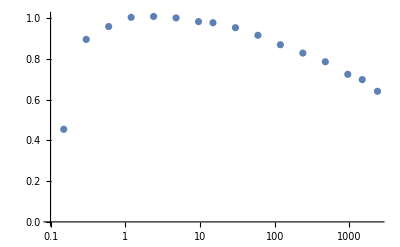

```mathematica
r = 0.3/2; (*cm*)
area = Pi*r^2;
planksconstant = 6.62607015*10^(−34);
speedoflight =299792458;
datanew = data;
datanew[[;;,1]]=datanew[[;;,1]] ;(* uW *) 
datanew[[;;,1]]=datanew[[;;,1]] /(area);(* uW/cm^2 *) 
datanew[[;;,1]]=(datanew[[;;,1]]*10^(-3)); (* W/cm^2 *) 
datanew[[;;,1]]=datanew[[;;,1]]/((planksconstant*speedoflight)/(525*10^(-9))); (* photons flux *)
datanew[[;;,1]]=datanew[[;;,1]]*extinction
ListLogLinearPlot[datanew[[3;;,{1,6}]]]
```

```mathematica
10^3
```

1000

```mathematica
13700*10^(-3)/((planksconstant*speedoflight)/(525*10^(-9)))*extinction
```

```mathematica
v.02
```

```mathematica
data2=Import["yb_dataset_2.csv","Data"];
data2[[;;,2]]=data2[[;;,2]]/Max[data2[[;;,2]]]; (* relative kex *) 
data2[[;;,1]]=data2[[;;,1]]; (*  kex *) 
(*data2[[;;,1]]=data2[[;;,1]]/(4.3*10^(-14)); (*  flux photons per meter *)  
data2[[;;,1]]=data2[[;;,1]]*((planksconstant*speedoflight)/(405*10^(-9)));*)
```

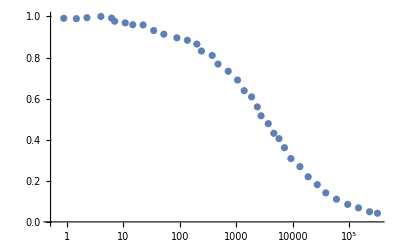

```mathematica
ListLogLinearPlot[data2,Joined->False]
```

```mathematica
(* -Graphics-https://pubs.acs.org/doi/10.1021/acs.jpcc.9b01296*)
```

{4.3×10^14,6.57819×10^14,9.08723×10^14,1.11444×10^15,1.29876×10^15,1.76387×10^15,2.23802×10^15,2.56418×10^15,3.14467×10^15,3.60296×10^15,4.41861×10^15,5.41891×10^15,6.87557×10^15,9.02563×10^15,1.12587×10^16,1.31208×10^16,1.78196×10^16,2.18537×10^16,2.59048×10^16,3.51819×10^16,4.46392×10^16,5.11447×10^16,7.1864×10^16,8.96444×10^16,1.11824×10^17,1.30318×10^17,1.80024×10^17,2.13395×10^17,2.57292×10^17,3.49434×10^17,4.3589×10^17,4.99414×10^17,7.01732×10^17,8.90367×10^17,1.12971×10^18,1.29435×10^18,1.72824×10^18,2.26868×10^18,2.68923×10^18,3.59072×10^18,4.47913×10^18,5.40051×10^18,6.73669×10^18,8.84331×10^18,1.12205×10^19,1.30762×10^19,1.74597×10^19,2.10512×10^19,2.671×10^19,3.56638×10^19,4.37375×10^19,5.54947×10^19,8.934×10^19,1.36673×10^20}

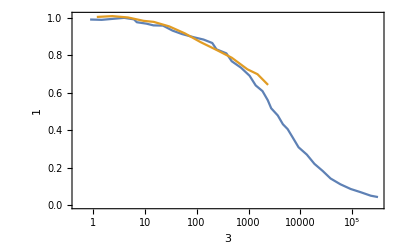

```mathematica
ListLogLinearPlot[{data2,datanew[[6;;,{1,6}]]},Joined->True,Frame->True,FrameLabel->{{"1","2"},{"3","4"}}]
```

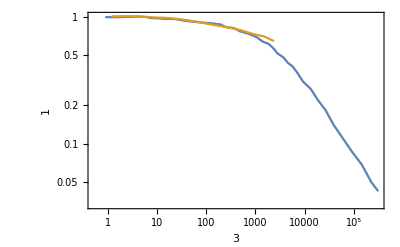

```mathematica
ListLogLogPlot[{data2,datanew[[6;;,{1,6}]]},Joined->True,Frame->True,FrameLabel->{{"1","2"},{"3","4"}}]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/tomikbaikie/Dropbox (Cambridge University)/Physics/Cambridge_Projects_To_Complete/LSC_Singlet_Fission/Figures/PLQE

```mathematica
Export["yb_processed.csv",data2]
Export["sf_processed.csv",datanew[[6;;,{1,6}]]]
```

yb_processed.csv

sf_processed.csv